## Initialisation

### fixed parameters

define ionisation potential, electric field amplitude  (intensity), fundamental wavelength...

```mathematica
ClearAll[Ip,ω,prefactor,r]
Ip=0.5;
ω = 0.057;
prefactor = ((ⅈ / Sqrt[π])*(2*Ip)^(1/4));
(*r={π/4,π/8,π/12}*)
(*r={π/4,π/6,π/8,π/10,π/12}*)
r={π/4,π/5,π/6,π/7,π/8,π/9,π/10,π/11,π/12,π/16,π/20,π/24,π/28,π/36,π/45,π/50,π/60,π/70,π/80,π/90,π/120,π/140,π/180,0}
```

{π/4,π/5,π/6,π/7,π/8,π/9,π/10,π/11,π/12,π/16,π/20,π/24,π/28,π/36,π/45,π/50,π/60,π/70,π/80,π/90,π/120,π/140,π/180,0}

### Define fields

electric  field  definition, vector potential, derivative of the action, action, ...

```mathematica
ClearAll[E1,Ax,Ay,A,Sf,Sfunc,DsFunc, D2sFunc,action]
(*Define the electric field function as a 2D vector*)
E1[t_,k_]:={Cos[k]*Cos[t]-Sin[k]* Cos[2 t],0};
(*Define the vector potential components*)
Ax[tx_,k_]:=-Integrate[E1[t,k][[1]],t]/. t->tx;
Ay[tx_,k_]:=-Integrate[E1[t,k][[2]],t]/. t->tx;
(*Define the 2D vector potential A*)
A[tx_,k_]:={Ax[tx,k],Ay[tx,k]};
Print[E1[t,k]]
Print[A[t,k]]

(*Define Sf,Sfunc,DsFunc,D2sFunc,and action in terms of px,Ax,py,and Ay*)
Sf[tk_,p_List,k_]=Integrate[2 (p[[1]]*Ax[t,k]+p[[2]]*Ay[t,k])+(Ax[t,k]^2+Ay[t,k]^2),t]/. t->tk;
Print[Sf[t,{px,py},k]]
Sfunc[t_,p_List,k_]:=0.5*Sf[t,p,k]+(0.5*(p[[1]]^2+p[[2]]^2)+Ip)*t;
Print[Sfunc[t,{px,py},k]]
DsFunc[t_,p_List,k_]:=D[Sfunc[tc,p,k],tc]/. tc->t;
Print[DsFunc[t,{px,py},k]]

D2sFunc[t_,p_List,k_]:=0.057*D[Sfunc[tz,p,k],{tz,2}]/. tz->t;
Print[D2sFunc[t,{px,py},k]]
D3sFunc[t_,p_List,k_]:=0.057*D[Sfunc[te,p,k],{te,3}]/. te->t;
Print[D3sFunc[t,{px,py},k]]
action[t_,p_List,k_]:=Exp[ⅈ*Sfunc[t,p,k]/0.057];
Print[action[t,{px,py},k]]
```

{Cos[k] Cos[t]-Cos[2 t] Sin[k],0}

{-Cos[k] Sin[t]+1/2 Sin[k] Sin[2 t],0}

Part::partd: Part specification p⟦1⟧ is longer than depth of object.

Part::partd: Part specification p⟦2⟧ is longer than depth of object.

1/96 (12 t Sin[k]^2+48 px (4 Cos[k] Cos[t]-Cos[2 t] Sin[k])-48 Cos[k] Sin[k] Sin[t]+48 Cos[k]^2 (t-Cos[t] Sin[t])+8 Sin[2 k] Sin[3 t]-3 Sin[k]^2 Sin[4 t])

(0.5+0.5 (px^2+py^2)) t+0.00520833 (12 t Sin[k]^2+48 px (4 Cos[k] Cos[t]-Cos[2 t] Sin[k])-48 Cos[k] Sin[k] Sin[t]+48 Cos[k]^2 (t-Cos[t] Sin[t])+8 Sin[2 k] Sin[3 t]-3 Sin[k]^2 Sin[4 t])

0.5+0.5 (px^2+py^2)+0.00520833 (-48 Cos[k] Cos[t] Sin[k]+12 Sin[k]^2-12 Cos[4 t] Sin[k]^2+24 Cos[3 t] Sin[2 k]+48 Cos[k]^2 (1-Cos[t]^2+Sin[t]^2)+48 px (-4 Cos[k] Sin[t]+2 Sin[k] Sin[2 t]))

0.000296875 (48 px (-4 Cos[k] Cos[t]+4 Cos[2 t] Sin[k])+192 Cos[k]^2 Cos[t] Sin[t]+48 Cos[k] Sin[k] Sin[t]-72 Sin[2 k] Sin[3 t]+48 Sin[k]^2 Sin[4 t])

0.000296875 (48 Cos[k] Cos[t] Sin[k]+192 Cos[4 t] Sin[k]^2-216 Cos[3 t] Sin[2 k]+48 Cos[k]^2 (4 Cos[t]^2-4 Sin[t]^2)+48 px (4 Cos[k] Sin[t]-8 Sin[k] Sin[2 t]))

ⅇ^((0.+17.5439 ⅈ) ((0.5+0.5 (px^2+py^2)) t+0.00520833 (12 t Sin[k]^2+48 px (4 Cos[k] Cos[t]-Cos[2 t] Sin[k])-48 Cos[k] Sin[k] Sin[t]+48 Cos[k]^2 (t-Cos[t] Sin[t])+8 Sin[2 k] Sin[3 t]-3 Sin[k]^2 Sin[4 t])))

### Define the momentum grid

```mathematica
ClearAll[pxValues,pyValues]
(*Define the range for px and py values*)
pxValues=Range[-3,3,0.1];
pyValues=Range[-3,3,0.1];
Print[Length[pxValues]]
Print[Length[pyValues]]
```

61

61

### Define plotting functions

```mathematica
ClearAll[plotEx,plotEy,plotRoots](*Plot Ex and Ey and roots*)
plotEx:=Quiet[Plot[E1[t][[1]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]]

plotEy:=Quiet[Plot[E1[t][[2]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ey"},ImageSize->Large]];

plotRoots[filteredTValues_]:=Quiet[ListPlot[{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]];
```

### Create Grid of Seeds

```mathematica
ClearAll[realMax,realMin,imagMax,imagMin,realSteps,imagSteps,listofseeds,initialGuess,listofseeds,seedPoints]
(*Generate the grid of seeds*) 

(*pick realmin to realmax as the range to capture the 4 saddle points in a periodic range of 2Pi*)
realMin=-2.133;realMax=4.150;
imagMin=0;imagMax=5;
realSteps=10;imagSteps=10;

listofseeds=Flatten[Table[x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}],1];

(*Add the specific initial guess to the list of seeds*)
initialGuess=-2.0334+1.2321 ⅈ;
listofseeds=Prepend[listofseeds,initialGuess];

(*Ensure seeds are numerical values*)
listofseeds=N[listofseeds];

(*Extract real and imaginary parts of the seeds*)
seedPoints={Re[#],Im[#]}&/@listofseeds;
```

Find  all  the  roots for all px and py values (saddle point solutions)

```mathematica
ClearAll[generatePlotAndRoots];

(*Function to generate plots and roots for given px and py*)
generatePlotAndRoots[px_,py_,seeds_,k_]:=
Module[
{allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues},
(*Find roots*)
allSolutions=Round[t/. Quiet[Table[FindRoot[DsFunc[t,{px,py},k]==0,{t,tseed}],{tseed,seeds}]],0.0001];
complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];
(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#,{px,py},k]]]<=tolerance&&Abs[Im[DsFunc[#,{px,py},k]]]<=tolerance&];
{filteredTValues}];
```

## CALCULATION : Saddle Point Solutions

```mathematica
Calculate all the time saddle point solutions value for corresponding px and py below
```

```mathematica
ClearAll[k]

DateString[]
(*Generate results using the precise px and py values*)
results=
(*ParallelTable works similarly to Table,but it distributes the computation across multiple CPU cores,allowing for parallel execution and significantly speeding up the process.*)
Table[ParallelTable[
generatePlotAndRoots[px,py,listofseeds,r[[i]]],
{px,pxValues}, {py,pyValues}
],{i,Length[r]}]
DateString[]
```

Wed 5 Mar 2025 13:13:27

$Aborted

Wed 5 Mar 2025 13:13:40

```mathematica
Print[Length[results]]
Print[Length[r]]
```

24

24

```mathematica
ClearAll[SaveToCell]
SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";
SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occurrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

```mathematica
SaveToCell[results,"results"]
```

```mathematica
results="results";
```

## REARRANGING SADDLE POINTS ARRAYS: px, py and mixing angle correctly indexed

```mathematica
ClearAll[newResults,pxValue,pyValue,tsExtended,validData, realAndImagTimes]
(*this now iterates over all different mixing angles as the calculations goes for one mixing angle all combinations of px and py will produce {{{px,py,{ts1,ts2,ts3,ts4}},different{px,py,{ts1,ts2,ts3,ts4}}, and so on} thats for the first r, now for the next mixing angle r[...}, and so on}. so hopefully this explains my iteration choices.*)
newResults=
Table[Table[{
(*Calculate pxValue based on the index i*)
pxValue=-3+(i-1)*0.1,
(*Calculate pyValue based on the index j*)
pyValue=-3+(j-1)*0.1,
(*Extract the corresponding results for the current px and py values*)
results[[q,i,j]]},
(*Iterate over the length of the results list for both i and j*)
{i,Length[results[[q]]]},{j,Length[results[[q]]]}
],{q,Length[r]}];

(*Flatten the newResults list by one level to get a list of sublists, Map over each sublist in flattenedResults For each sublist elem,join the first two elements with the elements of the nested list inside the third element.*)
tsExtended=Table[Map[Function[{elem},Join[{elem[[1]],elem[[2]]},elem[[3,1]]]],Flatten[newResults[[i]],1]],{i,Length[r]}];
(*so essentially grabbing px and py and putting them in the same array as the time saddle point solutions ts1,ts2,ts3,ts4 so the array of arrays will look like {{px,py,ts1,ts2,ts3,ts4},repeat for different values of px and py}*)


(*-validData is a list of lists of lists where each sublist contains four elements {Real part of ts,Imaginary part of ts,px,py}.*)
validData=
(*iterates over all mixing angles r so then it starts looking at the first r, which a list of list as described earlier in new results. and so on for all r values*)
Table[
(*Select elements from the list that satisfy a condition*)
Select[
(*Flatten the nested list into a list of lists*)
Flatten[
(*Generate a table of values*)
Table[
(*Conditional statement to check if the element is not Null*)
If[tsExtended[[q,i,j+2]]=!=Null,
{(*Real part of the complex number*)
Re[tsExtended[[q,i,j+2]]],
(*Imaginary part of the complex number*)
Im[tsExtended[[q,i,j+2]]],
(*px value*)
tsExtended[[q,i,1]],
(*py value*)
tsExtended[[q,i,2]]},
(*If the element is Null,return Nothing*)
Nothing],
(*Iterate over all rows of tsExtended*)
{i,Length[tsExtended[[q]]]},
(*Iterate over all columns except the first two, px and py.*)
{j,1,Length[tsExtended[[q,i]]]-2}],
(*-Flatten at level 1 converts the nested list into a list of lists*)
1],
(*-Select filters the flattened list to include only the elements where the first element is not Null*)
#[[1]]=!=Null&],
(*iterates over all mixing angles r*)
{q,Length[r]}];

(*(*length of valid data should be equal to the check solutions variable, if not there are missing saddle points as every saddle point px and py should have 4 saddle points*)
checksolutions1 = Length[pxValues]*Length[pyValues]*4*Length[r];
checksolutions2=Total[Table[Length[validData[[i]]], {i,Length[r]}]];
MissingSaddles=checksolutions1-checksolutions2;
Print["\n I should have ",checksolutions1,", Saddle points, but I have calculated/found ",checksolutions2,", So I have ",MissingSaddles," Missing Saddle Points."]
*)

(*Extract real and imaginary times from validData*)
realAndImagTimes=Table[validData[[q,All,1;;2]],{q,Length[r]}];
(*First need to iterate over all the mixing angles r, then [[All,1;;2]] is a part specification that extracts specific elements from each sublist. All indicates that we want to apply the extraction to all sublists in validData.   
1;;2 specifies the range of elements to extract from each sublist. In this case it extracts the first and second element [the real and imaginary parts of the saddle point solutions]*)
```

# PLOTTING: Complex Plane Time Saddle Points Indexed Momentum via Colour

```mathematica
(*Plot the time saddle points*)
Manipulate[
Column[
{Dynamic[Text[Style["Current r value: "<>ToString[r[[i]]],Bold,16]]],
ListPlot[
{realAndImagTimes[[i]]},
AxesLabel->{"Re","Im"},PlotRange->{{realMin,realMax},{imagMin,imagMax}},AspectRatio->1,GridLines->Automatic,PlotLabel->"Complex Time Plane: Saddle Points",ImageSize->Large]}],
{{i,1,"Index"},1,Length[r],1}
]
```

```mathematica
(*Plot the 3D graph with color representing py*)
Manipulate[
Column[
{Dynamic[Text[Style["Current r value: "<>ToString[r[[i]]],Bold,16]]],

ListPointPlot3D[{#[[1]],#[[2]],#[[3]]}&/@validData[[i]],ColorFunction->Function[{x,y,z},ColorData["Rainbow"][Rescale[z,{-3,3}]]],ColorFunctionScaling->False,AxesLabel->{"Real Time","Imaginary Time","px"},PlotLabel->"3D Data Representation",ImageSize->Large, PlotRange->{{realMin,realMax},{imagMin,imagMax}},(*ViewPoint->{5,-5,5}, ViewVertical->{0,0,1}*)ViewPoint->{0,0,10}, ViewVertical->{0,0,1} 
(*,PlotLegends->Placed[BarLegend[{"Rainbow",{-3,3}},LabelStyle->{FontSize->10},LegendLabel->"py"],{Right,Bottom}]*)]
}],
{{i,1,"Index"},1,Length[r],1}
]
(*comment i want to extract the indexed momentums px and py, for corresponding r mixing angle and the time saddle points arrays, to have one time array like realandimagtimes, and to have a momentum array which is correctly indexed according to realandimagtimes to look like {{{px1,py1},{px2,py2},{px3,py3}, and so on...},for different r{{px1,py1},{px2,py2},{px3,py3}, and so on...} for all values of r...}. and then essentially just plot the two correspondingly, would that make it less computationally taxing to plot then just iterating through valid data and plotting the values? *)
```

```mathematica
(*Plot the 3D graph with color representing py*)
Manipulate[
Column[
{Dynamic[Text[Style["Current r value: "<>ToString[r[[i]]],Bold,16]]],

ListPointPlot3D[{#[[1]],#[[2]],#[[4]]}&/@validData[[i]],ColorFunction->Function[{x,y,z},ColorData["Rainbow"][Rescale[z,{-3,3}]]],ColorFunctionScaling->False,AxesLabel->{"Real Time","Imaginary Time","py"},PlotLabel->"3D Data Representation",ImageSize->Large, PlotRange->{{realMin,realMax},{imagMin,imagMax}},(*ViewPoint->{5,-5,5}, ViewVertical->{0,0,1}*)ViewPoint->{0,0,10}, ViewVertical->{0,0,1} 
(*,PlotLegends->Placed[BarLegend[{"Rainbow",{-3,3}},LabelStyle->{FontSize->10},LegendLabel->"py"],{Right,Bottom}]*)]
}],
{{i,1,"Index"},1,Length[r],1}
]
(*comment i want to extract the indexed momentums px and py, for corresponding r mixing angle and the time saddle points arrays, to have one time array like realandimagtimes, and to have a momentum array which is correctly indexed according to realandimagtimes to look like {{{px1,py1},{px2,py2},{px3,py3}, and so on...},for different r{{px1,py1},{px2,py2},{px3,py3}, and so on...} for all values of r...}. and then essentially just plot the two correspondingly, would that make it less computationally taxing to plot then just iterating through valid data and plotting the values? *)
```

```mathematica
(*Preprocess the data to include colors based on the 4th component*)
data=Table[validData[[i]],{i,Length[r]}];
points=Table[{#[[1]],#[[2]],#[[4]]}&/@data[[i]],{i,Length[r]}];
colors=Table[ColorData["Rainbow"][Rescale[#[[3]],{-3,3}]]&/@data[[i]],{i,Length[r]}];
```

```mathematica
Manipulate[(*Create the 3D plot with precomputed colors*)
Graphics3D[{PointSize[Small],MapThread[{#2,Point[#1]}&,{points[[i]],colors[[i]]}]},Axes->True,AxesLabel->{"Real Time","Imaginary Time","px"},PlotLabel->"4D Data Representation",ImageSize->Full, PlotRange->{{realMin,realMax},{imagMin,imagMax},{-3,3}}, SphericalRegion->True,(*ViewPoint->{5,-5,5}, ViewVertical->{0,0,1},*)ViewPoint->{0,0,10}, ViewVertical->{0,0,1} 
],{i,Length[r]}]
```

### Extracting plots as mp4 videos

```mathematica
jheez=Table[(*Create the 3D plot with precomputed colors*)
Graphics3D[{PointSize[Small],MapThread[{#2,Point[#1]}&,{points[[i]],colors[[i]]}]},Axes->True,AxesLabel->{"Real Time","Imaginary Time","py"},PlotLabel->"4D Data Representation",ImageSize->Large, PlotRange->{{realMin,realMax},{imagMin,imagMax},{-3,3}}, SphericalRegion->True,(*ViewPoint->{5,-5,5}, ViewVertical->{0,0,1},*)ViewPoint->{0,0,10}, ViewVertical->{0,0,1} 
],{i,Length[r]}];
(*(Export the frames as an animation video)*) (*Export["jheez1.mp4",jheez,"FrameRate"->4]*)
```

# How to find fold points

struggling to find fold and cusp points, as there is a singular jacobian at point {t,py} and {t,py,px}, and find root fails to converge...

```mathematica
r[[10]]
```

### finding saddle points

```mathematica
Block[{px=0.5, py=0.01,k=10,tguess},
tguess=0.+1ⅈ;
FindRoot[DsFunc[t,{px,py},r[[k]]]==0,{t,tguess}]
]
```

{t→0.598704+1.17334 ⅈ}

### finding fold points

real and imaginary time, px and py. (4 variables) 4 equations real and imaginary parts of Dsfunc and D2Sfunc

```mathematica
Block[{ px=0.1,k=10,tguess, pyguess},
tguess=-2.0334+1.2321 ⅈ;
pyguess=0.1;
Table[FindRoot[
{DsFunc[t,{px,py},r[[k]]]==0,
D2sFunc[t,{px,py},r[[k]]]==0
},{t,tguess},{py,pyguess}],{tguess,listofseeds}]
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

### finding cusp points

```mathematica
Block[{ k=10,tguess, pyguess,pxguess},
tguess=-2.0334+1.2321 ⅈ;
pyguess=0.1;
pxguess=0.1;
Table[FindRoot[
{DsFunc[t,{px,py},r[[k]]]==0,
D2sFunc[t,{px,py},r[[k]]]==0,
D3sFunc[t,{px,py},r[[k]]]==0
},{t,tguess},{py,pyguess},{px,pxguess}],{tguess,listofseeds}]
];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

# FOLD POINT PLOTS? & more

```mathematica
r[[10]]
```

π/16

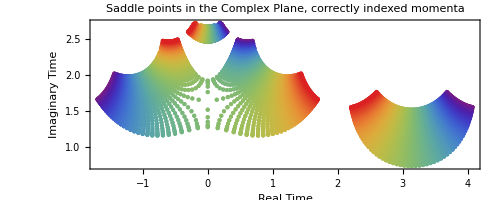

```mathematica
(*Preprocess the data to include colors based on the 3rd component*)
data1=validData[[10]];
points1={#[[1]],#[[2]]}&/@data1; (*Only use the first two components for 2D plotting*)

(*Check the range of the 4th component*)
minValue=Min[data1[[All,4]]];
maxValue=Max[data1[[All,4]]];
(*Print["Min value of 4th component: ",minValue];
Print["Max value of 4th component: ",maxValue];*)

colors1=ColorData["Rainbow"][Rescale[#[[3]],{minValue,maxValue}]]&/@data1;

(*(*Print the processed points and colors to verify*)
Print["Points: ",points1];
Print["Colors: ",colors1];*)

Graphics[{PointSize[Small],MapThread[{#2,Point[#1]}&,{points1,colors1}]},Frame->True,FrameLabel->{"Real Time","Imaginary Time"},PlotLabel->"Saddle points in the Complex Plane, correctly indexed momenta",ImageSize->Full,PlotRange->All]
```